# Arbitrary Spacing of Elements

```mathematica
$BaseSpacerSize=1;
$BaseObjectSize=1;
$DefaultColorGradient="DeepSeaColors";


LevelSpacerFunction[elementData_:{},level_Integer:1,lastInLevelInstanceQ_:False]:=
With[
{
adjustedLevel=If[lastInLevelInstanceQ, level-1, level]
(* Last element in current instance of level, needs spacing of previous level *)
},
If[adjustedLevel==0,$BaseSpacerSize,$BaseSpacerSize /adjustedLevel]
]

LevelSizeFunction[elementData_:{},level_Integer:1]:=$BaseObjectSize ;
LevelColorFunction[elementData_:{},level_Integer:1,absoluteIndex_Integer:1,relativeIndex_Integer:1,maxDepth_:1]:=ColorData[$DefaultColorGradient][level/maxDepth];
```

## Extract List Structure Data

```mathematica
ExtractListStructure::usage=StringJoin[
"ExtractListStructure[list] returns a list of tuples containing",
"{element, absolute index, level, relative index, last element at level instance}"
];
ExtractListStructure[ll_,atomQ_: Not@*ListQ]:=
Block[
{
i=1,
prev=None
},
Reap[
MapIndexed[
Function[
If[atomQ@#,
If[ListQ@prev,prev[[5]]=False;Sow@prev];
prev={#,i++,Length@#2,Last@#2, None},

If[ListQ@prev,prev[[5]]=True;Sow@prev;prev=None]
];
#
],ll,All
]
][[2,1]]
];
```

## Use extracted list structure to calculate spacing values

```mathematica
ClearAll[PositionTuple, PositionTuples]
PositionTuple[tuple_List,
spacingFunction_:LevelSpacerFunction,
sizingFunction_:LevelSizeFunction,
coloringFunction_:LevelColorFunction,
maxDepth_:1
]:=
With[
{
element=tuple[[1]],
absoluteIndex=tuple[[2]],
level=tuple[[3]],
relativeIndex=tuple[[4]],
lastInLevelInstanceQ=tuple[[5]]
},
Join[
tuple,
{
sizingFunction[element, level],
spacingFunction[element, level, lastInLevelInstanceQ],
0, (* aggregated spacing *)
coloringFunction[element,level, absoluteIndex,relativeIndex, maxDepth] 
}
]
]

PositionTuples[
extracted_List,
spacingFunction_:LevelSpacerFunction,
sizingFunction_:LevelSizeFunction,
coloringFunction_:LevelColorFunction
]:=
Module[
{maxDepth=Max@extracted[[;;,3]]},
Map[PositionTuple[#,spacingFunction,sizingFunction,coloringFunction,maxDepth]&, extracted]
]
(* element, index, level, lastElementInLevel, spacing, object size, aggregatedValue, color *)
```

## Aggregate Translations

```mathematica
AggregateTranslations[a_List,b_List]:=Join[b[[;;-3]],{ Total[a[[6;;8]]], b[[-1]]}]
```

## Example of how to integrate into bar chart

```mathematica
barChart[fl_List,horizontalQ_:True]:=
Map[
With[
{
color=#[[-1]],
size = #[[6]],
data=#[[1]],
aggregatedSpacer=#[[-2]]
},
With[
{
rectCoord=If[horizontalQ,{size,data}, {data, size}],
transCoord=If[horizontalQ,{aggregatedSpacer,0}, {0,aggregatedSpacer}]
},

Translate[
{color,
Rectangle[{0,0},rectCoord]
},
transCoord
]
]
]&,
fl
]
```

## Test all together

```mathematica
els=ExtractListStructure[{1,{2,2},3}];
apf = PositionTuples[els];
Join[{{"element","absolute index","level","relative index", "last in level instance","size","post spacing", "aggregation","color"}},apf]//TableForm
```

element | absolute index | level | relative index | last in level instance | size | post spacing | aggregation | color
1 | 1 | 1 | 1 | False | 1 | 1 | 0 | RGBColor[0.235431, 0.32765, 0.833291]
2 | 2 | 2 | 1 | False | 1 | 1/2 | 0 | RGBColor[0.772061, 0.92462, 0.998703]
2 | 3 | 2 | 2 | True | 1 | 1 | 0 | RGBColor[0.772061, 0.92462, 0.998703]
3 | 4 | 1 | 3 | True | 1 | 1 | 0 | RGBColor[0.235431, 0.32765, 0.833291]

```mathematica
fl=FoldList[AggregateTranslations,apf]
```

{{1,1,1,1,False,1,1,0,RGBColor[0.235431, 0.32765, 0.833291]},{2,2,2,1,False,1,1/2,2,RGBColor[0.772061, 0.92462, 0.998703]},{2,3,2,2,True,1,1,7/2,RGBColor[0.772061, 0.92462, 0.998703]},{3,4,1,3,True,1,1,11/2,RGBColor[0.235431, 0.32765, 0.833291]}}

```mathematica
bc=barChart[fl,True]
```

{Translate[{RGBColor[0.235431, 0.32765, 0.833291],Rectangle[{0,0},{1,1}]},{0,0}],Translate[{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{0,0},{1,2}]},{2,0}],Translate[{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{0,0},{1,2}]},{7/2,0}],Translate[{RGBColor[0.235431, 0.32765, 0.833291],Rectangle[{0,0},{1,3}]},{11/2,0}]}

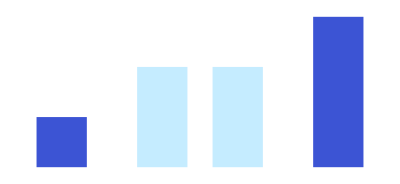

```mathematica
Graphics@bc
```

## ArbitrarilySpace

```mathematica
ArbitrarilySpace[
list_List,
spacingFunction_:LevelSpacerFunction,
sizingFunction_:LevelSizeFunction,
coloringFunction_:LevelColorFunction
]:=
FoldList[AggregateTranslations,PositionTuples[ExtractListStructure[list],spacingFunction,sizingFunction,coloringFunction]]
```

## Test

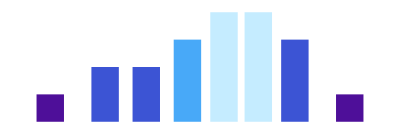

```mathematica
Graphics[barChart[ArbitrarilySpace[{1,{2,2,{3,{4,4}},3},1}],True]]
```

```mathematica
ArbitrarilySpace[{1,{2,2,{3,{4,4}},3},1}]
```

{{1,1,1,1,False,1,1,0,RGBColor[0.305814, 0.0607622, 0.601948]},{2,2,2,1,False,1,1/2,2,RGBColor[0.235431, 0.32765, 0.833291]},{2,3,2,2,False,1,1/2,7/2,RGBColor[0.235431, 0.32765, 0.833291]},{3,4,3,1,False,1,1/3,5,RGBColor[0.282325, 0.661868, 0.973082]},{4,5,4,1,False,1,1/4,19/3,RGBColor[0.772061, 0.92462, 0.998703]},{4,6,4,2,True,1,1/3,91/12,RGBColor[0.772061, 0.92462, 0.998703]},{3,7,2,4,True,1,1,107/12,RGBColor[0.235431, 0.32765, 0.833291]},{1,8,1,3,True,1,1,131/12,RGBColor[0.305814, 0.0607622, 0.601948]}}